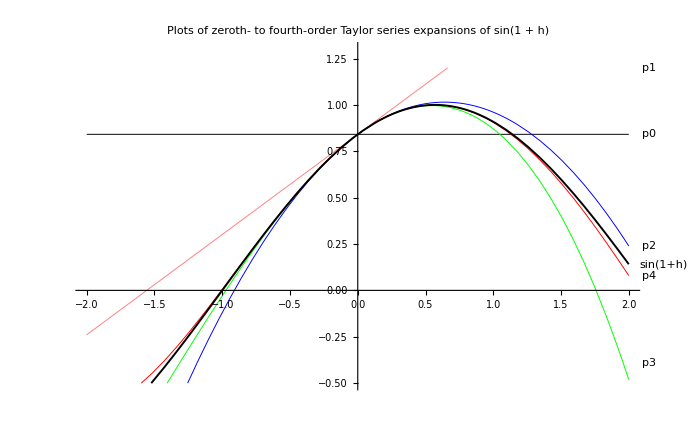

```mathematica
t=1;
p0=Sin[t];
p1=Sin[t]+h Cos[t];
p2=Sin[t]+h Cos[t]-h^2/2 Sin[t];
p3=Sin[t]+h Cos[t]-h^2/2 Sin[t]-h^3/6 Cos[t];
p4=Sin[t]+h Cos[t]-h^2/2 Sin[t]-h^3/6 Cos[t]+h^4/24 Sin[t];

plot1=Plot[p0,{h,-2,2}, PlotStyle->{Black, Thickness[0.001]},PlotLabels->Placed[Automatic,After],PlotRange->{{-2,2},{-0.5,1.2}}];
plot2=Plot[p1,{h,-2,2}, PlotStyle->{Pink, Thickness[0.001]},PlotLabels->Placed[Automatic,After],PlotRange->{{-2,2},{-0.5,1.2}}];
plot3=Plot[p2,{h,-2,2}, PlotStyle->{Blue, Thickness[0.001]},PlotLabels->Placed[Automatic,After],PlotRange->{{-2,2},{-0.5,1.2}}];
plot4=Plot[p3,{h,-2,2}, PlotStyle->{Green, Thickness[0.001]},PlotLabels->Placed[Automatic,After],PlotRange->{{-2,2},{-0.5,1.2}}];
plot5=Plot[p4,{h,-2,2}, PlotStyle->{Red, Thickness[0.001]},PlotLabels->Placed[Automatic,After],PlotRange->{{-2,2},{-0.5,1.2}}];
PLOT=Plot[Sin[1+h],{h,-2,2},PlotStyle->{Black,Thickness[0.002]} ,PlotLabels->Placed[Automatic,After],PlotRange->{{-2,2},{-0.5,1.2}}];
Show[plot1,plot2,plot3,plot4,plot5,PLOT,

PlotRange->{{-2,2},{-0.5,1.3}},
PlotLabel->"Plots of zeroth- to fourth-order Taylor series expansions of sin(1 + h)"]
```